```mathematica
(*Mathematica*)
```

```mathematica
(*Pisot polynomial sequence*)
```

```mathematica
Clear[p,q,x]
```

```mathematica
p[x_,1]=x-1
p[x_,2]=x^2-x-1
p[x_,3]=x^3-x-1
p[x_,4]=x^4-x^3-1
p[x_,5]=x^5-x^4-x^3+x^2-1
p[x_,6]=-1+x^2-x^4-x^5+x^6
p[x_,7]=-1+x^2-x^5-x^6+x^7
p[x_,8]=-1+x^2-x^6-x^7+x^8
```

-1+x

-1-x+x^2

-1-x+x^3

-1-x^3+x^4

-1+x^2-x^3-x^4+x^5

-1+x^2-x^4-x^5+x^6

-1+x^2-x^5-x^6+x^7

-1+x^2-x^6-x^7+x^8

```mathematica
w=Table[x/.NSolve[p[x,i]==0,x],{i,8}]
```

{{1.},{-0.618034,1.61803},{-0.662359-0.56228 ⅈ,-0.662359+0.56228 ⅈ,1.32472},{-0.819173,0.219447-0.914474 ⅈ,0.219447+0.914474 ⅈ,1.38028},{-0.831219-0.322384 ⅈ,-0.831219+0.322384 ⅈ,0.609585-0.707177 ⅈ,0.609585+0.707177 ⅈ,1.44327},{-0.845219,-0.577955-0.770016 ⅈ,-0.577955+0.770016 ⅈ,0.749767-0.536515 ⅈ,0.749767+0.536515 ⅈ,1.50159},{-0.868706-0.239062 ⅈ,-0.868706+0.239062 ⅈ,-0.212614-0.953977 ⅈ,-0.212614+0.953977 ⅈ,0.808713-0.424846 ⅈ,0.808713+0.424846 ⅈ,1.54522},{-0.863901,-0.769442-0.576296 ⅈ,-0.769442+0.576296 ⅈ,0.0758974-0.978449 ⅈ,0.0758974+0.978449 ⅈ,0.838656-0.350798 ⅈ,0.838656+0.350798 ⅈ,1.57368}}

```mathematica
(*Pisot hyperbolic 3 manifold root volumes*)
```

```mathematica
Table[Table[Im[PolyLog[2,w[[i,j]]]+Log[Abs[w[[i,j]]]] Log[1-w[[i,j]]]],{j,Length[w[[i]]]}],{i,Length[w]}]
```

{{Indeterminate},{0,0.},{-0.471354,0.471354,0.},{0,-0.981369,0.981369,0.},{-0.253721,0.253721,-0.995898,0.995898,0.},{0,-0.60839,0.60839,-0.915144,0.915144,0.},{-0.184967,0.184967,-0.828674,0.828674,-0.828441,0.828441,0.},{0,-0.434273,0.434273,-0.941162,0.941162,-0.752853,0.752853,0.}}

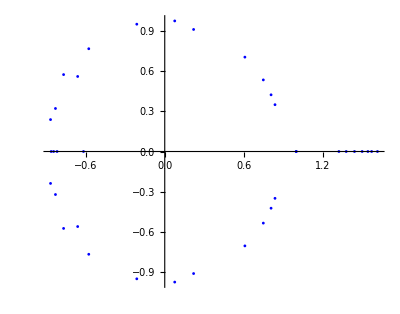

```mathematica
g1=Show[Table[ComplexListPlot[x/.NSolve[p[x,i]==0,x],PlotStyle->{PointSize[0.005],Blue},ImageSize->Full,PlotRange->All],{i,8}],PlotRange->All]
```

```mathematica
v=Flatten[Table[Table[If[Re[w[[i,j]]]>0&&Im[w[[i,j]]]==0,w[[i,j]],Nothing],{j,Length[w[[i]]]}],{i,Length[w]}]]
```

{1.,1.61803,1.32472,1.38028,1.44327,1.50159,1.54522,1.57368}

```mathematica
Clear[k]
```

```mathematica
(*Integer k root scaled Pisot polynomial*)
```

```mathematica
(*(obvious thatb they have integer coeffients if k is and integer)*)
```

```mathematica
u=Table[FullSimplify[ExpandAll[Product[x-k*w[[i,j]],{j,Length[w[[i]]]}]]]//Chop,{i,Length[w]}]
```

{-1. k+x,-1. k^2-1. k x+x^2,-1. k^3-1. k^2 x+x^3,-1. k^4-1. k x^3+x^4,-1. k^5+1. k^3 x^2-1. k^2 x^3-1. k x^4+x^5,-1. k^6+1. k^4 x^2-1. k^2 x^4-1. k x^5+x^6,-1. k^7+1. k^5 x^2-1. k^2 x^5-1. k x^6+x^7,-1. k^8+1. k^6 x^2-1. k^2 x^6-1. k x^7+x^8}

```mathematica
(*Beta integer scaled Pisot polynomials:inverses*)
```

```mathematica
wb=Table[u[[i]]/.k->1/v[[i]],{i,Length[u]}]
```

{-1.+x,-0.381966-0.618034 x+x^2,-0.43016-0.56984 x+x^3,-0.275508-0.724492 x^3+x^4,-0.159685+0.332628 x^2-0.480071 x^3-0.692872 x^4+x^5,-0.0872335+0.196693 x^2-0.443501 x^4-0.665959 x^5+x^6,-0.0475419+0.113515 x^2-0.418815 x^5-0.647159 x^6+x^7,-0.0265871+0.065842 x^2-0.403801 x^6-0.635454 x^7+x^8}

```mathematica
wbb=Table[x/.NSolve[wb[[i]]==0,x],{i,Length[wb]}]
```

{{1.},{-0.381966,1.},{-0.5-0.424452 ⅈ,-0.5+0.424452 ⅈ,1.},{-0.593484,0.158988-0.662529 ⅈ,0.158988+0.662529 ⅈ,1.},{-0.575928-0.223371 ⅈ,-0.575928+0.223371 ⅈ,0.422364-0.489983 ⅈ,0.422364+0.489983 ⅈ,1.},{-0.562881,-0.384894-0.512799 ⅈ,-0.384894+0.512799 ⅈ,0.499314-0.357297 ⅈ,0.499314+0.357297 ⅈ,1.},{-0.562191-0.154711 ⅈ,-0.562191+0.154711 ⅈ,-0.137595-0.617375 ⅈ,-0.137595+0.617375 ⅈ,0.523366-0.274943 ⅈ,0.523366+0.274943 ⅈ,1.},{-0.548969,-0.488945-0.366209 ⅈ,-0.488945+0.366209 ⅈ,0.0482293-0.621759 ⅈ,0.0482293+0.621759 ⅈ,0.532927-0.222916 ⅈ,0.532927+0.222916 ⅈ,1.}}

```mathematica
(*Inverse beta hyperPisot hyperbolic 3 manifold root volumes*)
```

```mathematica
Table[Table[Im[PolyLog[2,wbb[[i,j]]]+Log[Abs[wbb[[i,j]]]] Log[1-wbb[[i,j]]]],{j,Length[wbb[[i]]]}],{i,Length[wbb]}]
```

{{Indeterminate},{0,0},{-0.457233,0.457233,Indeterminate},{0,-0.938004,0.938004,Indeterminate},{-0.243798,0.243798,-0.907062,0.907062,0},{0,-0.584628,0.584628,-0.777201,0.777201,Indeterminate},{-0.175859,0.175859,-0.788464,0.788464,-0.653569,0.653569,0},{0,-0.414843,0.414843,-0.884431,0.884431,-0.556628,0.556628,2.79029×10^-15}}

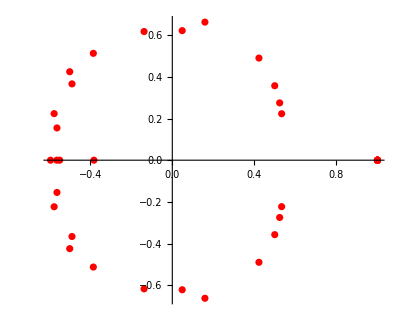

```mathematica
g2=Show[Table[ComplexListPlot[x/.NSolve[wb[[i]]==0,x],PlotStyle->Red,ImageSize->Full,PlotRange->All],{i,Length[wb]}],PlotRange->All]
```

```mathematica
wc=Table[u[[i]]/.k->v[[i]],{i,Length[u]}]
```

{-1.+x,-2.61803-1.61803 x+x^2,-2.32472-1.75488 x+x^3,-3.62966-1.38028 x^3+x^4,-6.26233+3.00636 x^2-2.08302 x^3-1.44327 x^4+x^5,-11.4635+5.08406 x^2-2.25479 x^4-1.50159 x^5+x^6,-21.0341+8.80938 x^2-2.38769 x^5-1.54522 x^6+x^7,-37.6122+15.1879 x^2-2.47647 x^6-1.57368 x^7+x^8}

```mathematica
wcc=Table[x/.NSolve[wc[[i]]==0,x],{i,Length[wb]}]
```

{{1.},{-1.,2.61803},{-0.877439-0.744862 ⅈ,-0.877439+0.744862 ⅈ,1.75488},{-1.13069,0.302898-1.26223 ⅈ,0.302898+1.26223 ⅈ,1.90517},{-1.19967-0.465287 ⅈ,-1.19967+0.465287 ⅈ,0.879795-1.02065 ⅈ,0.879795+1.02065 ⅈ,2.08302},{-1.26918,-0.867854-1.15625 ⅈ,-0.867854+1.15625 ⅈ,1.12585-0.805628 ⅈ,1.12585+0.805628 ⅈ,2.25479},{-1.34234-0.369403 ⅈ,-1.34234+0.369403 ⅈ,-0.328535-1.4741 ⅈ,-0.328535+1.4741 ⅈ,1.24964-0.656479 ⅈ,1.24964+0.656479 ⅈ,2.38769},{-1.3595,-1.21085-0.906905 ⅈ,-1.21085+0.906905 ⅈ,0.119438-1.53977 ⅈ,0.119438+1.53977 ⅈ,1.31977-0.552044 ⅈ,1.31977+0.552044 ⅈ,2.47647}}

```mathematica
(*beta hyper-Pisot hyperbolic 3 manifold root volumes*)
```

```mathematica
Table[Table[Im[PolyLog[2,wcc[[i,j]]]+Log[Abs[wcc[[i,j]]]] Log[1-wcc[[i,j]]]],{j,Length[wcc[[i]]]}],{i,Length[wcc]}]
```

{{Indeterminate},{0,0.},{-0.471354,0.471354,0.},{0,-0.961451,0.961451,0.},{-0.251387,0.251387,-0.952811,0.952811,0.},{0,-0.591947,0.591947,-0.847725,0.847725,0.},{-0.181686,0.181686,-0.795859,0.795859,-0.739659,0.739659,0.},{0,-0.420468,0.420468,-0.892697,0.892697,-0.64768,0.64768,0.}}

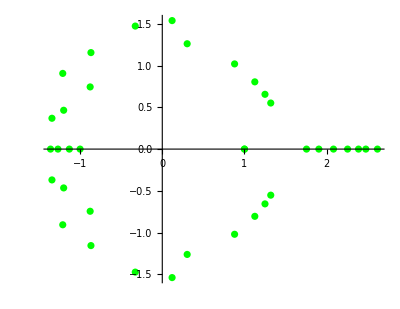

```mathematica
g3=Show[Table[ComplexListPlot[x/.NSolve[wc[[i]]==0,x],PlotStyle->Green,ImageSize->Full,PlotRange->All],{i,Length[wc]}],PlotRange->All]
```

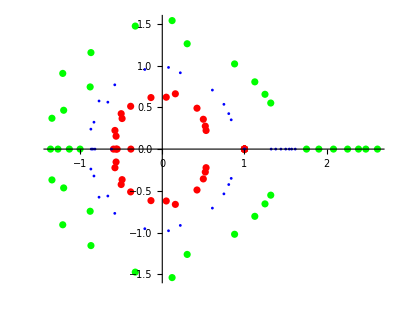

```mathematica
Show[{g3,g2,g1}]
```